```mathematica
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"];
```

```mathematica
ac = BinaryDeserialize[<<ac.bin];
labelled = BinaryDeserialize[Get[FileNameJoin[{NotebookDirectory[], "..", "labelled.bin"}]]];
components = BinaryDeserialize[<<components.bin];
```

```mathematica
summary[res_]:=Transpose[{Mean[ #], StandardDeviation[#]}& @ Transpose[res, {3, 1, 2}], {3, 1, 2}];
vspaces =Sort[  Keys[ac]];
```

```mathematica
AppendTo[$Path, NotebookDirectory[]];
cm = 72/2.54;
frameLabelStyle[text_]:= Style[text, FontSize->12,FontColor->Gray];
frameTicksStyle = Directive[FontSize-> 8, FontColor-> Gray];
legendStyle [text_]:= Style[text, FontSize->12, FontColor->Gray];
plotLabelStyle[text_]:= Style[text, FontSize->14, FontColor->Gray];
chartLabelStyle[text_]:=Style[text, FontSize-> 10, FontColor->Gray];
size= 8cm;
colorMap = 97;
thesisImages = FileNameJoin[{NotebookDirectory[],"..","..","..","thesis", "chapters", "img"}];
Needs["ErrorBarPlots`"];
SetDirectory[NotebookDirectory[]];
```

## Dimensionality Reduction

In order to classify the diffraction limited spots DFS into categories of used and unused, the region of interest around of each DF is represented as 11x11 image. Each image is scaled to that the minimum value is in the image is 0 and the maximum is 1.

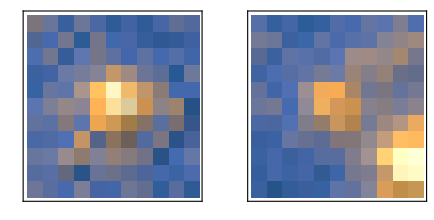

```mathematica
Block[{img},
img = GraphicsRow[{ReliefPlot[ArrayReshape[Keys[Select[labelled,Values[#1]==used&]⟦3⟧],{11,11}],PlotLegends->None,ImageSize->7cm],ReliefPlot[ArrayReshape[Keys[Select[labelled,Values[#1]==unused&]⟦4⟧],{11,11}],PlotLegends->None,ImageSize->7cm]}];
Export[FileNameJoin[{thesisImages, "refined-feature-example.pdf"}], img];
img]
```

## Calculate the reconstruction error

Since the data has very high dimensionality, 121 dimensions, training the classifier would require prohibitively large data set. Is it possible to avoid this problem by projecting the data to a lower dimensional space, by removing correlated dimensions.

The data is projected using Principal Component Analysis (PCA), which is a linear projection, and Auto-Encoder (AC), which is non-linear projection.

The data set is projected to 3 dimensions, with PCA and AC and visualised below.

```mathematica
Row[{
ListPointPlot3D[{
Keys[Select[compressed["AC 3"], Values[#] == used&]],Keys[Select[compressed["AC 3"], Values[#] == unused&]]
}, 
ImageSize->300,
PlotLegends->Placed[{"Used", "Unused"}, Below],
PlotLabel-> "Auto-Encoder"
],

ListPointPlot3D[{
Keys[Select[compressed["PCA 3"], Values[#] == used&]],
Keys[Select[compressed["PCA 3"], Values[#] == unused&]]
},
ImageSize->300,
PlotLegends->Placed[{"Used", "Unused"}, Below],
PlotLabel->"PCA"
]
}]
```

-Graphics3D--Graphics3D-

The data set is projected to 2, 3, 4, 5, 6, 8, 10, 12, 15, and 25 dimensions using both methods and for each projection the reconstruction error is calculated according

ℰ=1/N∑_(n=1)^N (x_n -r_n)^T.(x_n-r_n)

where x_n∈ℝ^121 is the n^thimage from the data set, reshaped as a vector, and r_n∈ℝ^121is the reconstruction of x_n.

```mathematica
{acTrain, acTest} = Get[FileNameJoin[{Directory[], "acData.bin"}]];
```

```mathematica
BinarySerialize[Eigenvectors[Covariance[acTrain]]]>>"components.bin"
```

```mathematica
resTest = {Transpose[{vspaces, Mean[#.#&/@(acTest - (acTest.Transpose[components[[1;;#]]]).components[[1;;#]] )]&/@vspaces}],
Transpose[{ vspaces, Mean[#.#& /@(acTest - ac[#][Trained]/@ acTest)]&/@ vspaces}]
};
```

```mathematica
resTrain = {Transpose[{vspaces,Mean[#.#&/@(acTrain- (acTrain.Transpose[components[[1;;#]]]).components[[1;;#]] )]&/@vspaces}],
Transpose[{ vspaces, Mean[#.#& /@(acTrain - ac[#][Trained]/@ acTrain)]&/@ vspaces}]
};
```

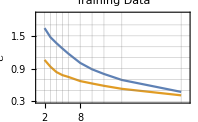
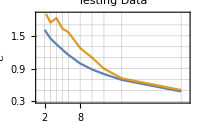

```mathematica
img = Column[{
Row[{
ListLinePlot[resTrain,
PlotLabel->plotLabelStyle["Training Data"],
Frame -> True,
FrameLabel->{
{frameLabelStyle@Rotate["ℰ", -Pi/2], None},
{frameLabelStyle@"Dimensionality", None}},
PlotRange->{{1,26},{0.3, 1.9}},
FrameTicksStyle->frameTicksStyle,
FrameTicks->{{Range[0.3, 1.8, 0.2],None}, {{2, 3, 4, 5, 6, 8, 10, 12, 15, 25},None}},
GridLines->{{2, 3, 4, 5, 6, 8, 10, 12, 15, 25}, Range[0.3, 1.8, 0.2]},
ImageSize->7cm,
PlotStyle->ColorData[colorMap]
],
ListLinePlot[resTest,
PlotLabel->plotLabelStyle["Testing Data"],
Frame -> True,
FrameLabel->{
{frameLabelStyle@Rotate["ℰ", -Pi/2], None},
{frameLabelStyle@"Dimensionality", None}},
PlotRange->{{1,26},{0.3, 1.9}},
FrameTicksStyle->frameTicksStyle,
FrameTicks->{{Range[0.3, 1.8, 0.2],None}, {{2, 3, 4, 5, 6, 8, 10, 12, 15, 25},None}},
GridLines->{{2, 3, 4, 5, 6, 8, 10, 12, 15, 25}, Range[0.3, 1.8, 0.2]},
ImageSize->7cm,
PlotStyle->ColorData[colorMap]
]
}],
SwatchLegend[ColorData[colorMap]/@{1, 2}, legendStyle/@{"PCA", "AC"}, LegendLayout->"Row"]
},
Alignment->Center
]
```

```mathematica
Export[FileNameJoin[{thesisImages,"background-reconstruction-error.pdf"}], img];
```

The reconstruction error is higher for the PCA  than AC on the training set, however on the testing set the reconstruction error is higher for the AC than PCA, which means that the AC over-fits the data. Therefore therefore PCA should be used for data compression and training the classifier.

```mathematica
Clear[acTrain, acTest, resTest, resTrain]
```

## Examine the results of the classification

For each projected data set a neural network with hidden units from 1 to 30 is trained 30 times and the training and testing accuracy is calculated. Each network is trained for 15000 epoch. The training algorithm is RMSProp and the initial weights are set to be random orthogonal matrix. Before training each network the data set is randomly shuffled and split to 70% training set and 30% testing set.

```mathematica
classifyResult = <|StringReplace[StringDrop[#, -4], "-"-> " "]-> If[FileExistsQ[#],  summary[BinaryDeserialize[<<(#)]], None]& /@ ("PCA-"<>ToString[#]<>".bin"&/@ #&@vspaces)|>;
```

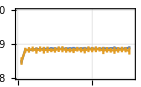
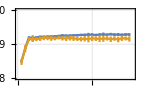
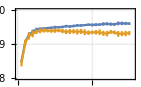
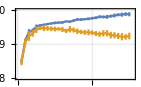
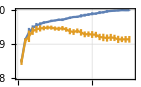
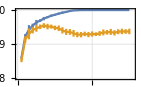
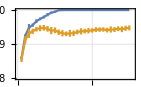
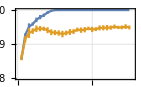
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- |  |

```mathematica
img = With[{
colors = {Blue, Orange},
PlotNNRes = Function[{dim},
ErrorListPlot[
classifyResult["PCA "<>ToString[dim]],
Joined->True,
PlotRange->{{0, 31},{0.80, 1.0}},
FrameTicksStyle->frameTicksStyle,
Frame-> True,
GridLines->Automatic,
PlotLabel->plotLabelStyle["Data Dim: "<>ToString[dim]],
ImageSize->5cm,
PlotStyle->ColorData[colorMap]
]
]
},Grid[Join[Partition[PlotNNRes/@ vspaces[[1;;-2]], 3], {{PlotNNRes[25], SwatchLegend[ColorData[colorMap]/@ {1, 2}, legendStyle/@{"Training Accuracy", "Testing Accuracy"}]}}]]
]
```

```mathematica
Export[FileNameJoin[{thesisImages,"background-classification-all.pdf"}], img];
```

```mathematica
Clear[img]
```

For projection the network with optimal number of hidden units is chosen. Then the average testing accuracy is plotted against the dimensionality of the projection for each method.

```mathematica
With[{pcaMaxHus=<|2->2 , 3->7 , 4-> 7, 5-> 6, 6-> 8, 8-> 7, 10->7 , 12-> 6, 15-> 5, 25-> 3|>},
Function[dim, {{dim, #1}, ErrorBar[#2]}& @@ classifyResult["PCA "<>ToString[dim]]⟦2,pcaMaxHus[dim]⟧]/@ vspaces]
```

{{{2,0.882163},ErrorBar[0.00731694]},{{3,0.918786},ErrorBar[0.0071851]},{{4,0.940576},ErrorBar[0.00643236]},{{5,0.947438},ErrorBar[0.0054622]},{{6,0.948608},ErrorBar[0.00591237]},{{8,0.954301},ErrorBar[0.00725596]},{{10,0.947944},ErrorBar[0.00827766]},{{12,0.945446},ErrorBar[0.00777498]},{{15,0.939184},ErrorBar[0.00755468]},{{25,0.926312},ErrorBar[0.0172826]}}

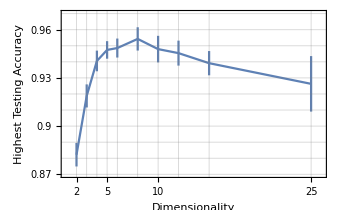

```mathematica
img = With[{pcaMaxHus=<|2->2 , 3->7 , 4-> 7, 5-> 6, 6-> 8, 8-> 7, 10->7 , 12-> 6, 15-> 5, 25-> 3|>},
ErrorListPlot[
Function[dim, {{dim, #1}, ErrorBar[#2]}& @@ classifyResult["PCA "<>ToString[dim]]⟦2,pcaMaxHus[dim]⟧]/@ vspaces
, Joined-> True,
FrameTicks->{{Range[0.87, 0.97, 0.01], None}, {vspaces, None}},
GridLines->{vspaces, Range[0.87, 0.97, 0.01]},
PlotRange->{{1, 26}, {0.87, 0.97}},
Frame-> True,
FrameTicksStyle->frameTicksStyle,
FrameLabel->(frameLabelStyle/@{"Dimensionality", "Highest Testing Accuracy"}),
ImageSize->12cm]]
```

```mathematica
Export[FileNameJoin[{thesisImages,"background-classification-summary.pdf"}], img];
```

```mathematica
Clear[img]
```

It appears that for both PCA and AC the best testing accuracy is for 8 dimensional data. For PCA this is then network with 7 hidden units is used and for AC this is when network with 6 hidden units is used.

Another useful result is the correlation between the training and testing accuracy over all samples.

```mathematica
pcaResults = <|{#-> BinaryDeserialize[Get["PCA-"<>ToString[#]<>".bin"]]} &/@ vspaces|>;
```

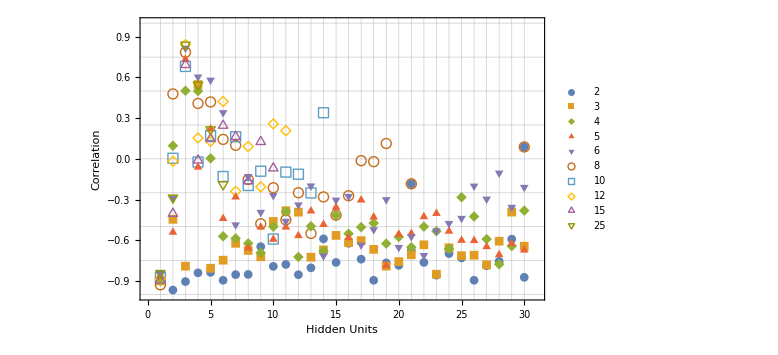

```mathematica
ListPlot[
Function[{dim},
({#1,Correlation[pcaResults[dim]⟦#1,All⟧][[1, 2]]}&)/@Range[1,30]
]/@ vspaces,
Frame-> True,
PlotMarkers->Automatic,
GridLines->{Range[1, 30, 1],Range[-1, 1, 0.25]},
PlotRange->{{0, 31},{-1, 1}},
FrameLabel->{"Hidden Units", "Correlation"},
PlotLegends->Placed[vspaces, Below],
ImageSize-> Large, PlotRange->{{0, 31}, {-1, 1}}]
```

I would expect a good model to have trained with sufficiently large data set to have low variance of training and testing accuracy and also very low correlation. If there is high correlation, that could be a sign that the number training iterations is insufficient, or  that the training algorithm is not very effective. Very strong anti-correlation could be a sign of over-fitting.

However the results show that models with 1 hidden unit almost always have very low correlation. On data sets with higher dimensionality than 3 models with 2 - 5 hidden units have very high correlation.

## Principal Components

```mathematica
Block[{img},
img = Grid[ArrayReshape[
ReliefPlot[
ArrayReshape[components⟦#⟧, {11, 11}],
FrameTicks->None,
ImageSize->3.5cm
]&/@Range[1, 20],{2, 4}]
];
Export[FileNameJoin[{thesisImages, "new-process-bg-pc.pdf"}], img];
img
]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Total[#[[1;;8]]]/Total@#&@Eigenvalues@Covariance@Keys@labelled
```

0.617924

```mathematica
{acTrain, acTest} = TakeDrop[
  Standardize[N[Keys[RandomSample[labelled]]], Mean, 1&],
  Floor[0.7 * Length[labelled]]
];
```

```mathematica
{acTrain, acTest} = TakeDrop[
  Standardize[N[Keys[RandomSample[labelled]]], Mean, 1&],
  Floor[0.7 * Length[labelled]]
];
```

```mathematica
BinarySerialize[{acTrain, acTest}]>>acData.bin
data = <||>;
rbms = <||>;

acEpoch = 10000;
epoch = 5000;
lrate = 0.01;
momentum = 0.9;

data[121] = acTrain;
```

```mathematica
AppendTo[$Path, FileNameJoin[{Directory[], ".." ,"..", "common"}]];
<<RBM`
```

```mathematica
(* Train rbms 121 -> 50 -> 25 *)
Print["Training RBM 50"];
rbms[50] = RBMTrain[50, data[121],
  LearningRate-> lrate,
  Momentum-> momentum,
  MaxTrainingRounds-> epoch];

Print["Training RBM 25"];
data[50] = RBMHiddenExpectation[rbms[50], data[121]];
rbms[25] = RBMTrain[25, data[50],
  LearningRate -> lrate,
  Momentum -> momentum,
  MaxTrainingRounds-> epoch];

data[25] = RBMHiddenExpectation[rbms[25], data[50]];

(* Train rbms 25 -> 12 -> 6 -> 3 *)
Print["Training RBM 12"];
rbms[12] = RBMTrain[12, data[25],
  LearningRate -> lrate,
  Momentum -> momentum,
  MaxTrainingRounds -> epoch];

Print["Training RBM 6"];
data[12] = RBMHiddenExpectation[rbms[12], data[25]];
rbms[6] = RBMTrain[6, data[12],
  LearningRate -> lrate,
  Momentum -> momentum,
  MaxTrainingRounds -> epoch];
```

Training RBM 50

Training RBM 25

$Aborted

Training RBM 12

Training RBM 6